# Simulations

## Parameters

```mathematica
(*cg=Quantity[15,"Millimolar"];(*glc in feed*)
Vg=Quantity[0.5,"Millimoles"/"Grams"/"Hours"];(*max glc uptake*)
R=Quantity[0.4,"Millimoles"/"Grams"/"Hours"];(*max uptake of pyruvate by mitochondria (max. respiration)*)
mE=Quantity[1,"Millimoles"/"Grams"/"Hours"];(*maintenance ATP demand*)
δlac=Quantity[0.002/2,1/"Millimolar"/"Hours"];(*lac death rate*)
y=1/Quantity[348,"Millimoles"/"Grams"];*)
```

```mathematica
(*cg=15.;Vg=0.5;R=0.9;y=1/348;δlac=0.0022;mE=1;
cg=15;Vg=0.5;R=0.8;y=1/348;δlac=0.005;mE=1;*)
cg=15.;Vg=0.5;R=0.4;(*y=1/348;*)δlac=0.0022/2;mE=1;
(*cg=15;Vg=0.5;R=0.8;y=1/348;δlac=0.;mE=1;*)
y=QuantityMagnitude[1/UnitConvert[Quantity[0.24393939393939396,"Moles"/"Grams"],"Millimoles"/"Grams"]];
{cg,Vg,R,y,δlac,mE}=Rationalize[{cg,Vg,R,y,δlac,mE}];
```

```mathematica
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[9/10,"Nanograms"]Quantity["Days"/"Milliliters"]);
```

## Functions

Basics

```mathematica
ClearAll[Mg,δ,λ,λmax,vl]
δ[sg_,sl_]:=δlac sl;
λ[sg_,sl_][vg_,vatp_]:=y(vatp-mE)-δ[sg,sl];
λmax[sg_,sl_,ξ_]:=λ[sg,sl][0.,vatpmax[ξ]]
Mg[ξ_]:=Piecewise[{{Vg, ξ≤cg/Vg}, {cg/ξ, ξ>cg/Vg}}];
vl[vg_,vatp_]:=1/19(vatp-40vg);
vo[vg_,vatp_]:=1/19(vatp-2vg);
vgmin[ξ_][vatp_]:=1/2 Max[1/20 vatp,vatp-19R];
vgmax[ξ_][vatp_]:=Min[Mg[ξ],1/2 vatp]
vatpmax[ξ_]:=2Mg[ξ]+19Min[2Mg[ξ],R]
polytope[ξ_][vg_,vatp_]:=Boole[0≤vg≤Mg[ξ]∧vl[vg,vatp]≤0∧0≤vo[vg,vatp]≤R]
polytopeother[ξ_][vg_,vatp_]:=Boole[0≤vatp≤vatpmax[ξ]∧vgmin[ξ][vatp]≤vg≤vgmax[ξ][vatp]];
polytope1[ξ_][vg_,vatp_]:=Boole[0≤vatp<Min[19R,2Mg[ξ]]∧1/38 vatp≤vg≤1/2 vatp]
polytope2[ξ_][vg_,vatp_]:=Boole[2Mg[ξ]≤vatp≤Min[19R,vatpmax[ξ]]∧1/38 vatp≤vg≤Mg[ξ]]
polytope3[ξ_][vg_,vatp_]:=Boole[19R≤vatp≤2Mg[ξ]∧1/2(vatp-18R)≤vg≤1/2 vatp]
polytope4[ξ_][vg_,vatp_]:=Boole[Max[19R,2Mg[ξ]]≤vatp≤vatpmax[ξ]∧1/2(vatp-18R)≤vg≤Mg[ξ]]
polysum[ξ_][vg_,vatp_]:=polytope1[ξ][vg,vatp]+polytope2[ξ][vg,vatp]+polytope3[ξ][vg,vatp]+polytope4[ξ][vg,vatp]
```

```mathematica
vertices[ξ_]:=If[vatpmax[ξ]>19R,
{{0,0},{2Mg[ξ],Mg[ξ]},{vatpmax[ξ],Mg[ξ]},{20R,R/2}},
{{0,0},{2Mg[ξ],Mg[ξ]},{vatpmax[ξ],Mg[ξ]}}]
```

Partition, expected values, variances, covariances

```mathematica
ClearAll[generateIntegral];

(* The integral in all the polytope *) 
generateIntegral[fun_,β_,ξ_,{atplb_,atpub_},{glbf_,gubf_}]:=Module[{int0,int1,lb,ub},
int1=Simplify@Integrate[Exp[-β y(vatpmax[ξ]-vatp)]fun[vg,vatp],
{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
int0=Simplify@Integrate[fun[vg,vatp],{vatp,atplb,atpub},{vg,glbf[ξ,vatp],gubf[ξ,vatp]},Assumptions->{atplb,atpub}∈Reals];
Piecewise[{{0, atplb≥atpub}, {int1, β>0}, {int0, β==0}}]];
generateIntegral[1][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{0,Min[20R,2Mg[ξ]]},{{ξ,vatp}↦vatp/40,{ξ,vatp}↦vatp/2}];
generateIntegral[2][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{2Mg[ξ],Min[20R,vatpmax[ξ]]},{{ξ,vatp}↦vatp/40,{ξ,vatp}↦Mg[ξ]}];
generateIntegral[3][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{20R,2Mg[ξ]},{{ξ,vatp}↦1/2(vatp-19R),{ξ,vatp}↦1/2 vatp}];
generateIntegral[4][fun_,β_,ξ_]:=generateIntegral[fun,β,ξ,{Max[20R,2Mg[ξ]],vatpmax[ξ]},{{ξ,vatp}↦1/2(vatp-19R),{ξ,vatp}↦Mg[ξ]}];
```

```mathematica
ClearAll[fourDef]
fourDef[symbol_,fun_,norm_]:=Module[{},
ClearAll[symbol];
Do[symbol[i,β_,ξ_]:=Evaluate@generateIntegral[i][fun,β,ξ],{i,4}];
symbol[β_,ξ_]:=Sum[symbol[i,β,ξ],{i,4}]/norm[β,ξ]]
```

```mathematica
fourDef[z,{vg,vatp}↦1,{β,ξ}↦1];
fourDef[expVatp,{vg,vatp}↦vatp,z];
fourDef[expVg,{vg,vatp}↦vg,z];
```

```mathematica
expVl[β_,ξ_]:=1/19(expVatp[β,ξ]-40expVg[β,ξ]);
```

```mathematica
(*fourDef[mom2Vatp,{vg,vatp}↦vatp^2,z];
fourDef[mom2Vg,{vg,vatp}↦vg^2,z];
fourDef[mom2Vl,{vg,vatp}↦vl[vg,vatp]^2,z];
varVg[β_,ξ_]:=mom2Vg[β,ξ]-expVg[β,ξ]^2;
varVatp[β_,ξ_]:=mom2Vatp[β,ξ]-expVatp[β,ξ]^2;
varVl[β_,ξ_]:=mom2Vl[β,ξ]-expVl[β,ξ]^2;*)
```

```mathematica
(*(*fourDef[expVgVatp,{vg,vatp}↦vg vatp,z];
covVgVatp[β_,ξ_]:=expVgVatp[β,ξ]-expVg[β,ξ]expVatp[β,ξ];*)*)
```

```mathematica
ClearAll[pVatp,pVglc,pVglcVatp]
Do[pVatp[i,β_,ξ_,vatp0_]:=Evaluate@generateIntegral[i][{vg,vatp}↦DiracDelta[vatp-vatp0],β,ξ],{i,4}];
pVatp[β_,ξ_,vatp0_]:=Sum[pVatp[i,β,ξ,vatp0],{i,4}]/z[β,ξ];
pVglcVatp[β_,ξ_,vatp0_,vglc0_]:=pVatp[β,ξ,vatp0] Boole[vgmin[ξ][vatp0]≤vglc0≤vgmax[ξ][vatp0]]/(vgmax[ξ][vatp0]-vgmin[ξ][vatp0])
pVglc[β_,ξ_,vg0_]:=Evaluate@Integrate[pVglcVatp[β,ξ,vatp,vg0],{vatp,2vg0,19Min[R,2vg0]+2vg0}]
```

```mathematica
pVglc[β_,ξ_]:=pVglc[β,ξ]={vg}↦Evaluate[Integrate[pVglcVatp[β,ξ,vatp,vg],{vatp,2vg,19Min[R,2vg]+2vg}]]
```

```mathematica
(*Do[pVglc[i,β_,ξ_,vg0_]:=Evaluate@generateIntegral[i][{vg,vatp}↦DiracDelta[vg-vg0],β,ξ],{i,4}];
pVglc[β_,ξ_,vg0_]:=Sum[pVgc[i,β,ξ,vg0],{i,4}]/z[β,ξ];*)
```

```mathematica
(*Do[pVlac[i,β_,ξ_,vl0_]:=Evaluate@generateIntegral[i][{vg,vatp}↦DiracDelta[vl[vg,vatp]-vl0],β,ξ],{i,4}];
pVlac[β_,ξ_,vo0_]:=Sum[pVlac[i,β,ξ,vo0],{i,4}]/z[β,ξ];*)
```

```mathematica
(*Do[pVox[i,β_,ξ_,vo0_]:=Evaluate@generateIntegral[i][{vg,vatp}↦DiracDelta[vo[vg,vatp]-vo0],β,ξ],{i,4}];
pVox[β_,ξ_,vo0_]:=Sum[pVox[i,β,ξ,vo0],{i,4}]/z[β,ξ];*)
```

```mathematica
(*ClearAll[pVg]
Do[pVg[i,β_,ξ_,v_]:=Evaluate@generateIntegral[i][{vg,vatp}↦DiracDelta[vg-v],β,ξ],{i,4}];
pVg[β_,ξ_,v_]:=Sum[pVg[i,β,ξ,v],{i,4}]/z[β,ξ]*)
```

```mathematica
NIntegrate[pVglc[2.,10.][v],{v,0,1/2}]
```

1.

β = ∞ model (be sure to run this AFTER the previous cells)

```mathematica
expVg[∞,ξ_]:=Mg[ξ];
expVatp[∞,ξ_]:=vatpmax[ξ];
expVo[∞,ξ_]:=Min[2expVg[∞,ξ],R];
expVl[∞,ξ_]:=expVo[∞,ξ]-2expVg[∞,ξ];
```

Equilibrium

```mathematica
sgeq[β_,ξ_]:=cg-ξ expVg[β,ξ]
sleq[β_,ξ_]:=-ξ expVl[β,ξ]
Deq[β_,ξ_]:=λ[sgeq[β,ξ],sleq[β,ξ]][expVg[β,ξ],expVatp[β,ξ]]
Xeq[β_,ξ_]:=Deq[β,ξ]ξ
```

```mathematica
Assert[False]
```

```mathematica
ClearAll[ξmax,ξ1,ξ2,ξDlocMax,ξDlocMin,ξDlocMinMax];On[Assert];
ξmax[β_]:=ξmax[β]=Module[{ξ},ξ/.First[Quiet[FindRoot[Deq[β,ξ]==0,{ξ,0.1,40 cg/mE}]]]];
(*ξDlocMax[β_]:=ξDlocMax[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β]},Assert[ξ0≤ξm];If[ξ0<ξm,FindMaximum[Deq[β,ξ],{ξ,ξm}],ξm]];*)
ξDlocMinMax[β_]:=ξDlocMinMax[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β],ξ1,ξ2},
Assert[ξ0≤ξm];
If[ξ0==ξm,Return[{ξ0,ξm}]];
ξ1=Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ0,ξ0,ξm}];
ξ2=Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξm,ξ0,ξm}];
If[Not[ξ0<ξ1<ξm∨ξ0<ξ2<ξm],Return[{ξm,ξ0}]];
If[ξ1==ξ0||ξ1==ξm,ξ1=Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ2,ξ0,ξ2}]];
If[ξ2==ξ0||ξ2==ξm,ξ2=Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξ1,ξ1,ξm}]];
Return[{ξ1,ξ2}];
]
ξDlocMin[β_]:=ξDlocMin[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β]},Assert[ξ0≤ξm];If[ξ0<ξm,Last@Last@Last@FindMinimum[Deq[β,ξ],{ξ,ξ0,ξ0,ξm}],ξ0]];
ξDlocMax[β_]:=ξDlocMax[β]=Module[{ξ,ξ0=ξmax[0],ξm=ξmax[β]},Assert[ξ0≤ξm];If[ξ0<ξm,Last@Last@Last@FindMaximum[Deq[β,ξ],{ξ,ξm,ξ0,ξm}],ξm]];
ξDlocMin[β_]:=ξDlocMinMax[β]⟦1⟧;
ξDlocMax[β_]:=ξDlocMinMax[β]⟦2⟧;
```

Leave this plot here to explain the meanings of ξ1,ξ2

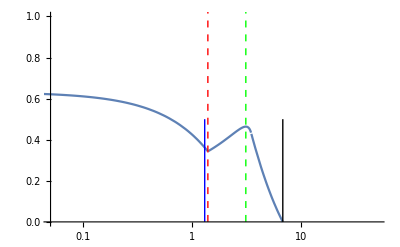

```mathematica
Module[{β=10/(vatpmax[0]y)},LogLinearPlot[Deq[β,ξ/ξunit]24,{ξ,0.0001,ξmax[β]ξunit},PlotRange->{{0.05,50},{0,1}},FrameLabel->{"ξ (10^6 cells·day/mL)","D (1/day)"},
Epilog->{
RGBColor[0, 0, 1],Line[{{Log[ξmax[0]ξunit],0},{Log[ξmax[0]ξunit],0.5}}],
GrayLevel[0],Line[{{Log[ξmax[β]ξunit],0},{Log[ξmax[β]ξunit],0.5}}],
RGBColor[0, 1, 0],Dashed,Line[{{Log[ξDlocMax[β]ξunit],0},{Log[ξDlocMax[β]ξunit],15}}],
RGBColor[1, 0, 0],Dashed,Line[{{Log[ξDlocMin[β]ξunit],0},{Log[ξDlocMin[β]ξunit],15}}]}]]
```

## Figure of critical ξs

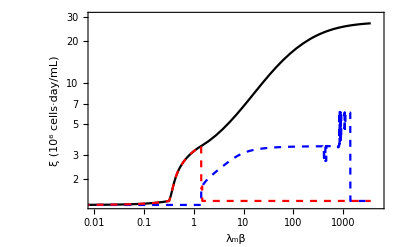

```mathematica
LogLogPlot[{ξmax[β/(vatpmax[0]y)]ξunit,ξDlocMax[β/(vatpmax[0]y)]ξunit,ξDlocMin[β/(vatpmax[0]y)]ξunit},{β,0.025vatpmax[0]y,100000vatpmax[0]y},Frame->True,LabelStyle->Directive[Black,12],FrameLabel->{"λ_mβ","ξ (10^6 cells·day/mL)"},PlotRange->{{0.01,0.5 10^4},{0,1.1ξmax[∞]ξunit}},WorkingPrecision->20,PlotStyle->{GrayLevel[0],Directive[RGBColor[0, 0, 1],Dashed],Directive[RGBColor[1, 0, 0],Dashed]},FrameStyle->GrayLevel[0],PlotStyle->GrayLevel[0]]
(*Export[NotebookDirectory[]<>"../fig/xi-critical.pdf",%]*)
```

```mathematica
BarLegend[{ColorData["Rainbow"][#/(2.15 1.1111)]&,{0,2.15 1.1111}},LabelStyle->Directive[GrayLevel[0],12]]
```

```mathematica
Export[NotebookDirectory[]<>"../fig/xi-critical-gradient-barlegend.pdf",BarLegend[{ColorData["Rainbow"][#/(2.15 1.1111)]&,{0,2.15 1.1111}},LabelStyle->Directive[GrayLevel[0],12]]]
```

/home/cossio/work/maxent-chemostat/mathematica/../fig/xi-critical-gradient-barlegend.pdf

```mathematica
Xeqmem[β_,ξ_]:=Xeqmem[β,ξ]=Xeq[β,ξ];
XeqFeas[β_,ξ_]:=Piecewise[{{Xeqmem[β,ξ], ξ<ξmax[β]}, {0, True}}];
Show[
ListDensityPlot[
N[Function[{β,ξ},{β,ξ,XeqFeas[β/(vatpmax[0]y),ξ/ξunit]}]@@@Tuples[{Exp@Range[Log[25/1000 vatpmax[0]y],Log[100000vatpmax[0]y],1/10],Range[9/10,11/10 ξmax[∞]ξunit,1/10]}],12],
PlotLegends->Automatic,InterpolationOrder->0,PlotRange->Full,ScalingFunctions->{"Log","Log",None},
FrameLabel->{"λ_mβ","ξ_m (10^6 cells·day/mL)"},LabelStyle->Directive[GrayLevel[0],12],
ColorFunction->(Piecewise[{{GrayLevel[1],#==0},{ColorData["Rainbow"][#/2.15],True}}]&),ColorFunctionScaling->False,PlotRangeClipping->True,FrameStyle->GrayLevel[0]],
LogLogPlot[{ξmax[β/(vatpmax[0]y)]ξunit},{β,0.025vatpmax[0]y,100000vatpmax[0]y},Frame->True,LabelStyle->Directive[GrayLevel[0],12],FrameLabel->{"λ_mβ","ξ_m (10^6 cells·day/mL)"},PlotRange->{{0.01,0.5 10^4},{0,1.1ξmax[∞]ξunit}},WorkingPrecision->20,PlotStyle->{Directive[GrayLevel[0],Thick]}]]
Export[NotebookDirectory[]<>"../fig/xi-critical-gradient.pdf",%]
```

-Graphics-

/home/cossio/work/maxent-chemostat/mathematica/../fig/xi-critical-gradient.pdf

```mathematica
$HistoryLength
```

```mathematica
{0,1.1ξmax[∞]ξunit}
```

{0,30.5556}

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[…]

```mathematica
DensityPlot[Xeq[β/(vatpmax[0]y),ξ ξunit],{β,0.01,0.5 10^4},{ξ,0,1.1ξmax[∞]ξunit},ScalingFunctions->{"Log","Log"},PlotLegends->Automatic]
```

## Simulations

```mathematica
LogLinearPlot[{Max[0,Xeq[β,10]],Max[0,Xeq[β,20]]},{β,0.1,1000000},PlotRange->{0.01,1.},Frame->True,FrameLabel->{"β","X"},
PlotLegends->Placed[LineLegend[{"ξ=10","ξ=20"}],{0.15,.8}]]
Export[NotebookDirectory[]<>"../fig/X-beta-notox.png",%];
```

-Graphics-

```mathematica
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[9/10,"Nanograms"]Quantity["Days"/"Milliliters"])
```

5/108

```mathematica
vatpmax[0]y//N
```

0.0352547

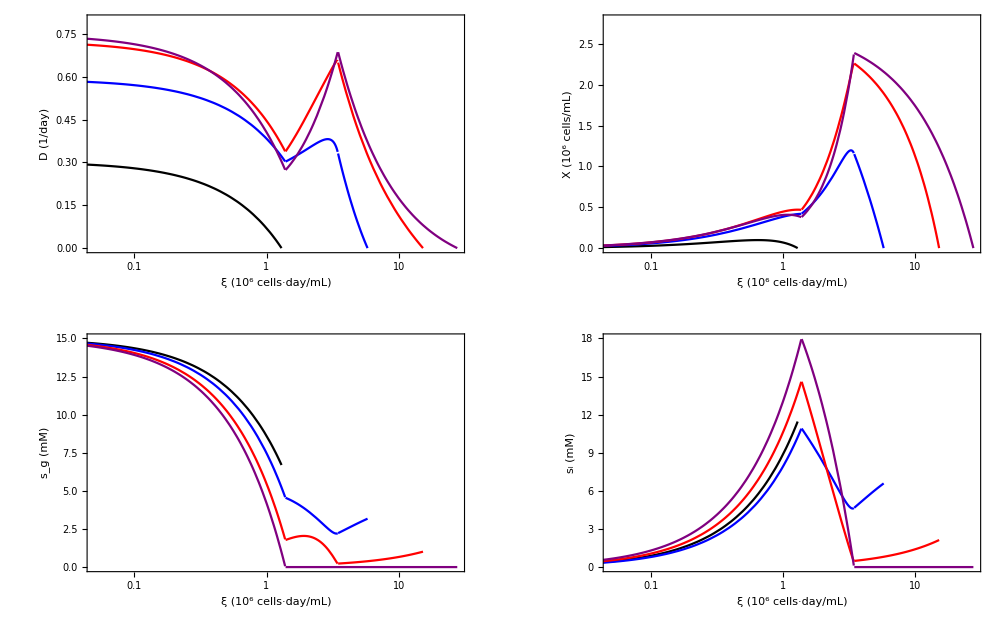

```mathematica
Module[{grid,βlist,colorList,plot,plotopts,ξunit,ξrange},
ξunit=(10^-6 Quantity["Grams"/"Liters""Hours"])/(Quantity[0.9,"Nanograms"]Quantity["Days"/"Milliliters"]);
βlist={0,1.99 100,1.99 1000,∞};colorList={GrayLevel[0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5]};
plotopts={PlotRange->Full,Frame->True,LabelStyle->Directive[GrayLevel[0],12],FrameStyle->GrayLevel[0],GridLines->None,Axes->None};
ξrange={-3,Log[ξmax[∞]ξunit]};
grid=GraphicsGrid[{
{Show[Table[LogLinearPlot[Deq[βlist⟦i⟧,ξ/ξunit]24,{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","D (1/day)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,0.8}}],
Show[Table[LogLinearPlot[Xeq[βlist⟦i⟧,ξ/ξunit]1.111111,{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","X (10^6 cells/mL)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,2.8}}]},
{Show[Table[LogLinearPlot[sgeq[βlist⟦i⟧,ξ/ξunit],{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","s_g (mM)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,15}}],
Show[Table[LogLinearPlot[sleq[βlist⟦i⟧,ξ/ξunit],{ξ,0.0001,ξmax[βlist⟦i⟧]ξunit},Evaluate@plotopts,FrameLabel->{"ξ (10^6 cells·day/mL)","s_l (mM)"},PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{ξrange,{0,18}}]}},
ImageSize->1000];
plot=Legended[grid,LineLegend[colorList,Table["λ_mβ = "<>ToString@NumberForm[N[β vatpmax[0]y],2],{β,βlist}]]];
Export[NotebookDirectory[]<>"../fig/xi-eqs-tox-w.pdf",plot];plot]
```

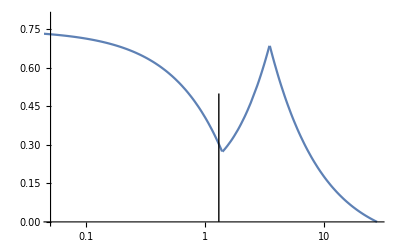

```mathematica
Module[{β=∞},LogLinearPlot[Deq[β,ξ/ξunit]24,{ξ,0.0001,ξmax[β]ξunit},PlotRange->{{0.05,28},{0,0.8}},FrameLabel->{"ξ (10^6 cells·day/mL)","D (1/day)"},Epilog->{Line[{{Log[ξmax[0]ξunit],0},{Log[ξmax[0]ξunit],0.5}}]}]]
```

```mathematica
ξmax[0]ξunit
```

1.29928

```mathematica
ξ2[100]
```

30.

```mathematica
{ξmax[0],ξ1[100],ξmax[100]}
```

{28.0644,52.3285,96.8147}

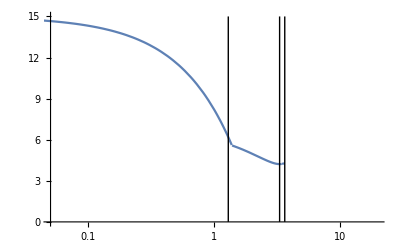

```mathematica
Module[{β=50},LogLinearPlot[sgeq[β,ξ/ξunit],{ξ,0.0001,ξmax[β]ξunit},PlotRange->{{0.05,20},{0,15}},FrameLabel->{"ξ (10^6 cells·day/mL)","s_g (mM)"},Epilog->{Line[{{Log[ξmax[0]ξunit],0},{Log[ξmax[0]ξunit],15}}],
Line[{{Log[ξmax[β]ξunit],0},{Log[ξmax[β]ξunit],15}}],
Line[{{Log[ξ1[50]ξunit],0},{Log[ξ1[50]ξunit],15}}]}]]
```

```mathematica
Deq[0,1.2/ξunit]24
```

0.0231166

```mathematica
ToString[NumberForm[N[1000 vatpmax[0]y],2]]
```

35.

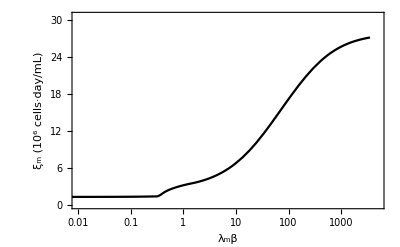

```mathematica
LogLinearPlot[ξmax[β/(vatpmax[0]y)]ξunit,{β,0.025vatpmax[0]y,100000vatpmax[0]y},Frame->True,LabelStyle->Directive[Black,12],FrameLabel->{"λ_mβ","ξ_m (10^6 cells·day/mL)"},PlotRange->{{0.01,0.5 10^4},{0,1.1ξmax[∞]ξunit}},FrameStyle->GrayLevel[0],PlotStyle->GrayLevel[0]]
Export[NotebookDirectory[]<>"../fig/beta-xi-notox.pdf",%];
```

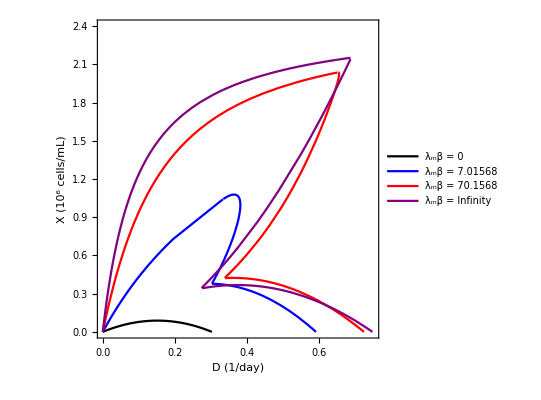

```mathematica
Module[{βlist,colorList,plot,leg},
βlist={0,1.99 100,1.99 1000,∞};colorList={GrayLevel[0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5]};
plot=Show[Table[ParametricPlot[{24Deq[βlist⟦i⟧,ξ],Xeq[βlist⟦i⟧,ξ]},{ξ,0,ξmax[βlist⟦i⟧]},AspectRatio->1,PlotRange->Full,Frame->True,FrameLabel->{"D (1/day)","X (10^6 cells/mL)"},FrameStyle->GrayLevel[0],GridLines->None,Axes->None,PlotStyle->colorList⟦i⟧],
{i,Length@βlist}],PlotRange->{{0,0.75},{0,2.4}}];
leg=Legended[plot,LineLegend[colorList,Table["λ_mβ = "<>ToString[β vatpmax[0]y],{β,βlist}]]];
Export[NotebookDirectory[]<>"../fig/bif-diagram.pdf",leg];leg]
```

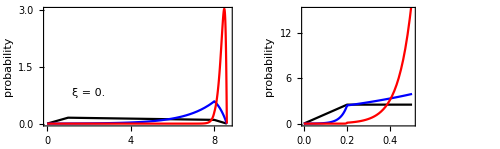

```mathematica
Module[{βlist,colorList,grid,leg,ξ},
ξ=0.;βlist={0,1.99 100,1.99 1000,∞};colorList={GrayLevel[0],RGBColor[0, 0, 1],RGBColor[1, 0, 0],RGBColor[0.5, 0, 0.5]};
grid=GraphicsGrid[
{{
Show[Table[Plot[pVatp[βlist⟦i⟧,ξ,v],{v,0,vatpmax[ξ]},PlotRange->Full,Frame->True,FrameLabel->{"v_atp (mmol/h/gDW)","probability"},FrameStyle->GrayLevel[0],GridLines->None,Axes->None,PlotStyle->colorList⟦i⟧],
{i,Select[Range[Length@βlist],ξ≤ξmax[βlist⟦#⟧]&]}],
PlotRange->{{0,vatpmax[ξ]1.01},{0,3}},
Epilog->Style[Text["ξ = "<>ToString[ξ],{2,0.8}],14]],

Show[Table[pVglc[βlist⟦i⟧,ξ];Plot[pVglc[βlist⟦i⟧,ξ][v],{v,0,vgmax[ξ][vatpmax[ξ]]},PlotRange->Full,Frame->True,FrameLabel->{"v_glc (mmol/h/gDW)","probability"},FrameStyle->GrayLevel[0],GridLines->None,Axes->None,PlotStyle->colorList⟦i⟧],
{i,Select[Range[Length@βlist],ξ≤ξmax[βlist⟦#⟧]&]}],
PlotRange->{{0,vgmax[ξ][vatpmax[ξ]]1.01},{0,15}},
Epilog->Style[Text["ξ = "<>ToString[ξ/ξunit],{2,0.8}],14]]
}}
,ImageSize->500];
leg=Legended[grid,LineLegend[colorList,Table["λ_mβ = "<>ToString[β vatpmax[0]y],{β,βlist}]]];
Export[NotebookDirectory[]<>StringTemplate["../fig/Pv-notox-ξ=``.pdf"][ξ],leg];leg]
```

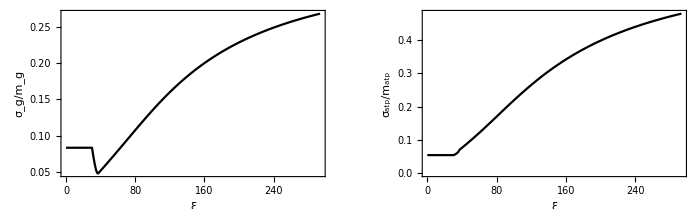

```mathematica
Module[{β=500,ξ0,ξ1},
ξ0=0;ξ1=ξmax[β];
GraphicsGrid[{{
Plot[{(√varVg[β,ξ])/expVg[β,ξ]},{ξ,ξ0,ξ1},Frame->True,FrameLabel->{"ξ","σ_g/m_g"},PlotStyle->GrayLevel[0]],
Plot[{(√varVatp[β,ξ])/expVatp[β,ξ]},{ξ,ξ0,ξ1},Frame->True,FrameLabel->{"ξ","σ_atp/m_atp"},PlotStyle->GrayLevel[0]]}},ImageSize->700]]
Export[NotebookDirectory[]<>"../fig/std-notox.png",%];
```

# Polytope

```mathematica
Solve[vatpmax[ξ]==19R,ξ]//N
```

{{ξ→37.5}}

```mathematica
vertices[1]//N
```

{{0.,0.},{1.,0.5},{8.6,0.5},{8.,0.2}}

```mathematica
10ξunit
```

0.462963

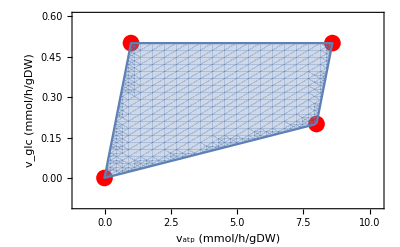

/home/cossio/W/maxent-chemostat/mathematica/../fig/polytope.pdf

```mathematica
Module[{ξ=10,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-1,1.2vatpmax[ξ]},{-0.1,1.2Mg[ξ]}},
FrameLabel->{"v_atp (mmol/h/gDW)","v_glc (mmol/h/gDW)"},Frame->True,PlotRange->{{0,10},{0,0.6}},Axes->False],
RegionPlot[polytope[ξ][vg,vatp]==1,{vatp,0,vatpmax[ξ]},{vg,0,Mg[ξ]}]]]
Export[NotebookDirectory[]<>"../fig/polytope.pdf",%]
```

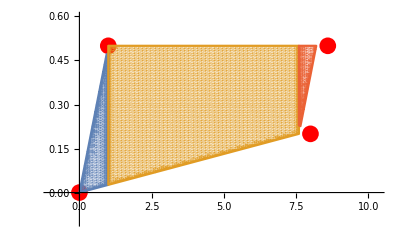

```mathematica
Module[{ξ=0.01,population,path},
Show[
ListPlot[vertices[ξ],PlotStyle->Directive[RGBColor[1, 0, 0],PointSize[0.03]],PlotRange->{{-1,1.2vatpmax[ξ]},{-0.1,1.2Mg[ξ]}}],
RegionPlot[{polytope1[ξ][vg,vatp]==1,polytope2[ξ][vg,vatp]==1,polytope3[ξ][vg,vatp]==1,polytope4[ξ][vg,vatp]==1},{vatp,0,vatpmax[ξ]},{vg,0,Mg[ξ]},PlotPoints->60,MaxRecursion->5]]]
```